```mathematica
SetOptions[Plot, 
  BaseStyle -> {FontSize -> 20}
  ];

SetOptions[ParametricPlot, 
  BaseStyle -> {FontSize -> 20}
  ];
  
SetOptions[ComplexPlot3D, 
  BaseStyle -> {FontSize -> 14}
  ];
```

## SISTEMAS DE PRIMEIRA ORDEM

```mathematica
O1F=TransferFunctionModel[{{1/(s+1)}},s];
O1=StateSpaceModel@O1F;
```

```mathematica
ComplexPlot3D[1/(s+1),{s,-2-2I,2+2I},PlotLegends->Automatic, PlotRange-> {0,5}]
```

-Graphics3D-

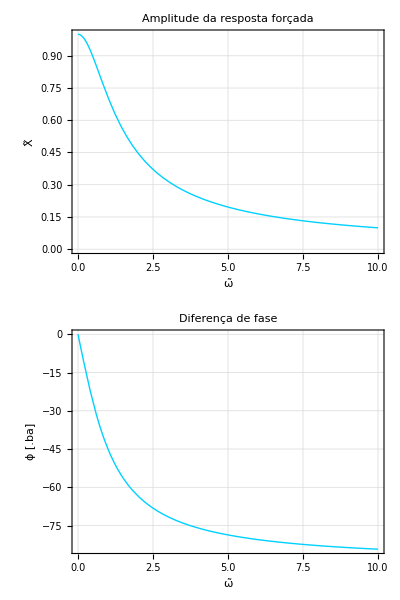

```mathematica
FRO1[foo_,range_,label_,ylabel_]:=
Plot[
(*Abs*)foo[1/(s+1)/.{s-> ⅈ ω}],
{ω,0,10},
PlotRange->range(*{0,+3}*),

PlotStyle->{Hue@(0.53),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃",ylabel},
PlotLabel->label,

ImageSize->{450,450},
AspectRatio->1
]

{{FRO1[Abs,{0,+1},"Amplitude da resposta forçada","X̃"],
FRO1[Arg[#]180/π&,{1,-91},"Diferença de fase","ϕ [.ba]"]}}//Transpose//TableForm
```

```mathematica
OutputResponse[O1, Sin[ω t],t]//FullSimplify
```

{(ⅇ^-t ω-ω Cos[t ω]+Sin[t ω])/(1+ω^2)}

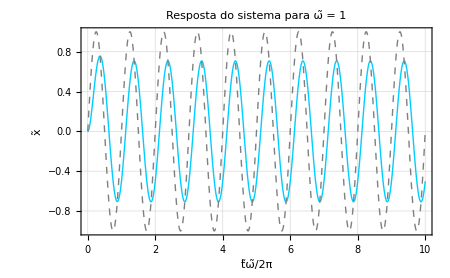

```mathematica
ORO1[ω_]:=Block[{response,plot},
plot=(response=OutputResponse[O1, Sin[ω t], {t,0,10 2π/ω}];
Plot[
response/.{t->2π τ/ω },
{τ,0,10},
PlotRange-> {-1,+1},
PlotStyle->{Hue@(√(√2/5)),Thick},
GridLines->Automatic,
Frame->True,
FrameLabel->{"t̃ω̃/2π","x̃"},
PlotLabel->StringForm["Resposta do sistema para ω̃ = ``",ω],
ImageSize->{450,450}
]
);
Show @@( Flatten @ {
plot,
{Plot[
Sin[2π τ],
{τ,0,10},
PlotRange-> {-1,+1},
PlotStyle->{Gray,Dashed,Thick}]}
})
]
ORO1[1]
```

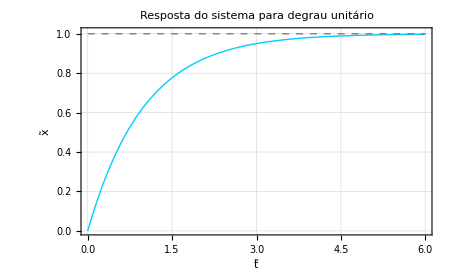

```mathematica
Block[{response,plot},
plot=(response=OutputResponse[O1,UnitStep[t], {t,0,20}];
Plot[
response,
{t,0,6},
PlotStyle->{Hue@(√(√2/5)),Thick},
PlotRange-> {0,+1.01},
GridLines->Automatic,
Frame->True,
FrameLabel->{"t̃","x̃"},
PlotLabel->StringForm["Resposta do sistema para degrau unitário",ω],
ImageSize->{450,450}
]
);
Show @@( Flatten @ {
plot,
{Plot[
UnitStep[t],
{t,0,6},
PlotStyle->{Gray,Dashed,Thick}]}
})
]
```

```mathematica
OutputResponse[O1,UnitStep[t], {t,0,20}]/.t->{1,2,3,4,5,6,7}
```

{{0.632121,0.864665,0.950213,0.981684,0.993262,0.997521,0.999088}}

## SISTEMAS DE SEGUNDA ORDEM

### POLOS

```mathematica
O2F=TransferFunctionModel[{{1/(s^2+2 ζ s+1)}},s];
O2=StateSpaceModel@O2F;
```

```mathematica
Manipulate[
ComplexPlot3D[1/(s^2+2 ζ s+1)/.{ζ->zt},{s,-2-2I,2+2I},PlotLegends->Automatic, PlotRange->{0,5}],
{{zt,0},-2,2}
]
```

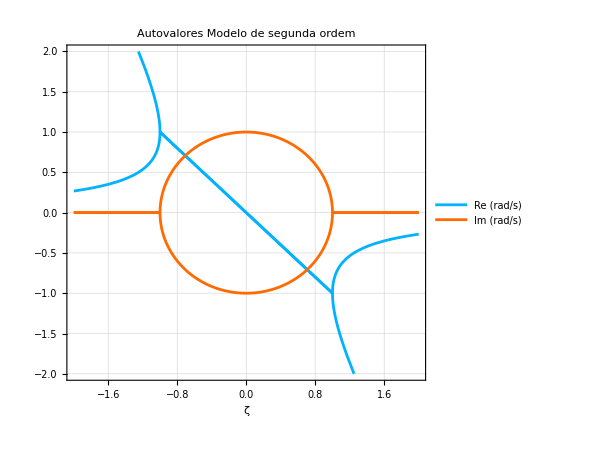

```mathematica
Show[

Plot[
Sort@(Re/@Eigenvalues[O2⟦1,1⟧]),
{ζ,-2,+2},
PlotRange->{-2,+2},

PlotStyle->Hue[0.55],

GridLines->Automatic,

Frame->True,
FrameLabel->{"ζ",None},
PlotLabel->"Autovalores \n Modelo de segunda ordem",
PlotLegends->Placed[
 LineLegend[{"Re (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],

ImageSize->{450,450},
AspectRatio->1
],

Plot[
Sort@Chop@(*Abs@*)(Im/@Eigenvalues[O2⟦1,1⟧]),
{ζ,-2,2},

PlotStyle->Hue[0.07],

PlotLegends-> Placed[
 LineLegend[{"Im (rad/s)"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
]
]

]
```

```mathematica
Show[
ParametricPlot[
{{Re[-ζ-√(-1+ζ^2)],Im[-ζ+√(-1+ζ^2)]},{Re[-ζ+√(-1+ζ^2)],-Im[ζ+√(-1+ζ^2)]}}(*MapThread[List,{Sort@(Re/@Eigenvalues[O2⟦1,1⟧]),Sort@RedundantElim@Chop@(*Abs@*)(Im/@Eigenvalues[O2⟦1,1⟧])}]*),
{ζ,-200,+200},
PlotRange->{-1.2,+1.2},
PlotPoints->100000,

PlotStyle->{Hue[0.55],Hue[1]},

GridLines->Automatic,

Frame->True,
FrameLabel->{"Re","Im"},
PlotLabel->"Lugar da raízes \n Modelo de segunda ordem",

ImageSize->{450,450},
AspectRatio->1
]/.Line[x_]:>{Arrowheads[Table[.01,{250}]],Arrow[x]},
ListPlot[{{0,-1},{0,+1}},PlotMarkers->{"ζ=0 \n"},PlotStyle->Gray],
ListPlot[{{-1,0}},PlotMarkers->{"ζ=1 \n"},PlotStyle->Red],
ListPlot[{{+1,0}},PlotMarkers->{"ζ=-1 \n"},PlotStyle->Magenta],
ListPlot[{{0,0}},PlotMarkers->{"ζ=±∞ \n"},PlotStyle-> Darker[Green]]
]
```

-Graphics-

### RESPOSTA EM FREQUÊNCIA

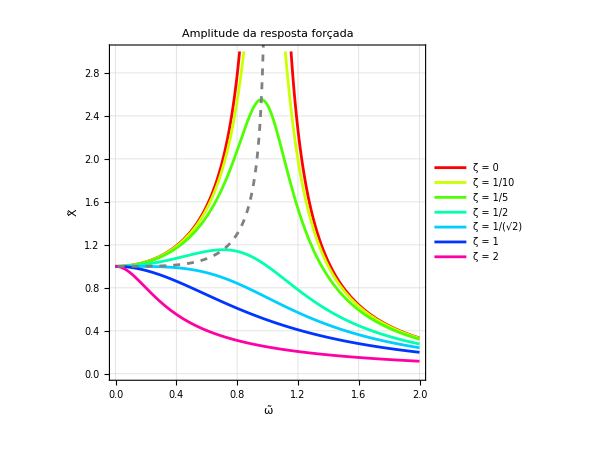
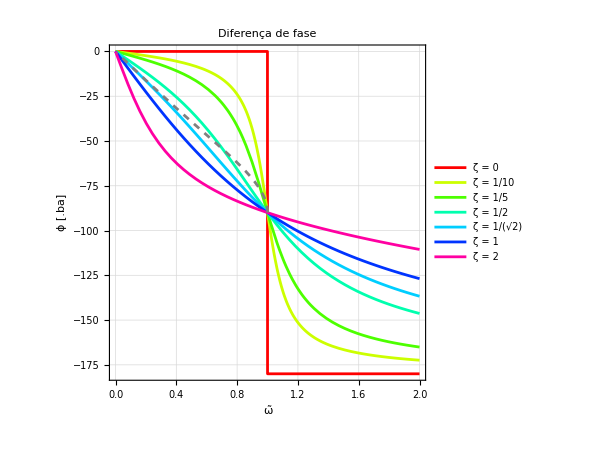

```mathematica
FRO2[foo_,range_,label_,ylabel_,legends_:False]:=Show @@( Flatten @ {
Plot[
(*Abs*)foo[1/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]/.ζ->(#+10^-12),
{ω,0,2},
PlotRange->range(*{0,+3}*),

PlotStyle->{Hue@(√(#/2.5)),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃",ylabel},
PlotLabel->label,
PlotLegends->If[legends,
Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
{}
],

ImageSize->{450,450},
AspectRatio->1
]&/@{0,1/10,1/5,1/2,√2/2,1,2},
{ParametricPlot[
{ω,(*Abs*)foo[1/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]}/.ω->√(1-2 ζ^2),
{ζ,0,2},
PlotStyle->{Gray,Dashed}
]}
}
)

{{FRO2[Abs,{0,+3},"Amplitude da resposta forçada","X̃",True],
FRO2[Arg[#]180/π&,{0.1,-180.1},"Diferença de fase","ϕ [.ba]",True]}}//Transpose//TableForm
```

```mathematica
Solve[D[1/(√(1-2 ω^2+4 ζ^2 ω^2+ω^4)),ω]==0,{ω}]
```

{{ω→0},{ω→-√(1-2 ζ^2)},{ω→√(1-2 ζ^2)}}

### RESPOSTA EM FREQUÊNCIA - MOVIMENTO RELATIVO

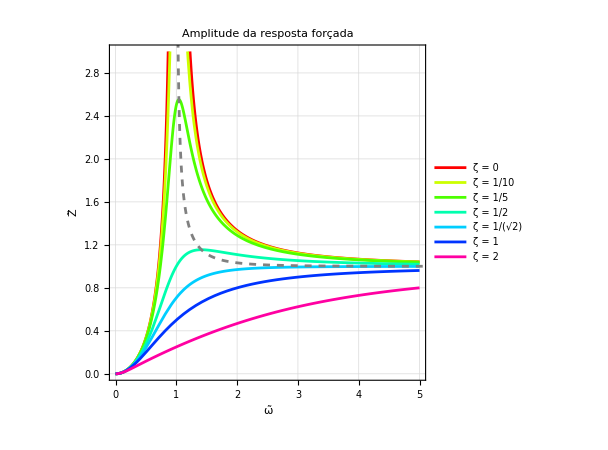
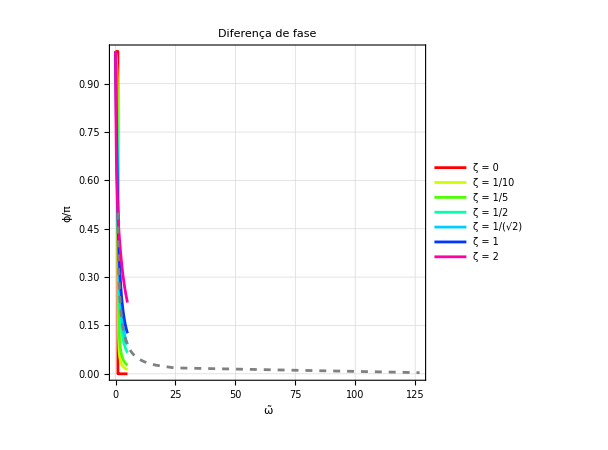

```mathematica
FRO22[foo_,range_,label_,ylabel_,legends_:False]:=Show @@( Flatten @ {
Plot[
(*Abs*)foo[s^2/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]/.ζ->(#+10^-12),
{ω,0,5},
PlotRange->range(*{0,+3}*),

PlotStyle->{Hue@(√(#/2.5)),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃",ylabel},
PlotLabel->label,
PlotLegends->If[legends,
Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
{}
],

ImageSize->{450,450},
AspectRatio->1
]&/@{0,1/10,1/5,1/2,√2/2,1,2},
{ParametricPlot[
{ω,(*Abs*)foo[s^2/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]}/.ω->1/(√(1-2 ζ^2)),
{ζ,0,2},
PlotStyle->{Gray,Dashed}
]}
}
)
{{FRO22[Abs,{0,+3},"Amplitude da resposta forçada","Z̃",True],
FRO22[Arg[#]/π&,{1.01,-0.01},"Diferença de fase","ϕ/π",True]}}//Transpose//TableForm
```

```mathematica
Solve[D[ω^2/(√(1-2 ω^2+4 ζ^2 ω^2+ω^4)),ω]==0,{ω}]
```

{{ω→0},{ω→-1/(√(1-2 ζ^2))},{ω→1/(√(1-2 ζ^2))}}

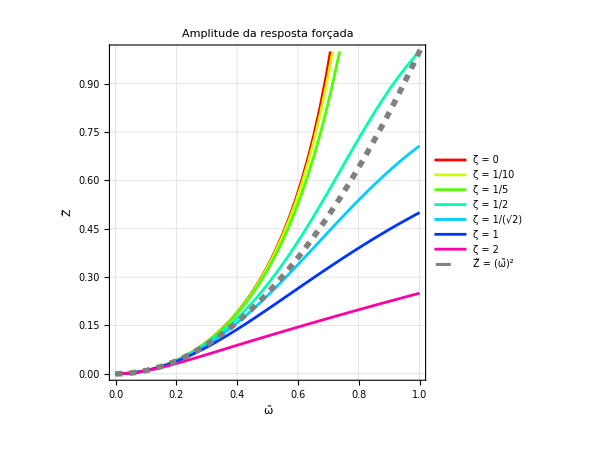

```mathematica
Show @@( Flatten @ {
Plot[
(*Abs*)Abs[s^2/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]/.ζ->(#+10^-12),
{ω,0,1},
PlotRange->{0,1},

PlotStyle->{Hue@(√(#/2.5)),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃","Z̃"},
PlotLabel->"Amplitude da resposta forçada",
PlotLegends->Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],

ImageSize->{450,450},
AspectRatio->1
]&/@{0,1/10,1/5,1/2,√2/2,1,2},
{Plot[
ω^2,
{ω,0,2},
PlotStyle->{Gray,Thickness[0.009],Dashed},
PlotLegends->Placed[
 LineLegend[{"Z̃ = (ω̃)^2"},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
]
]}
}
)
```

### RESPOSTA EM FREQUÊNCIA - BASE VIBRANTE

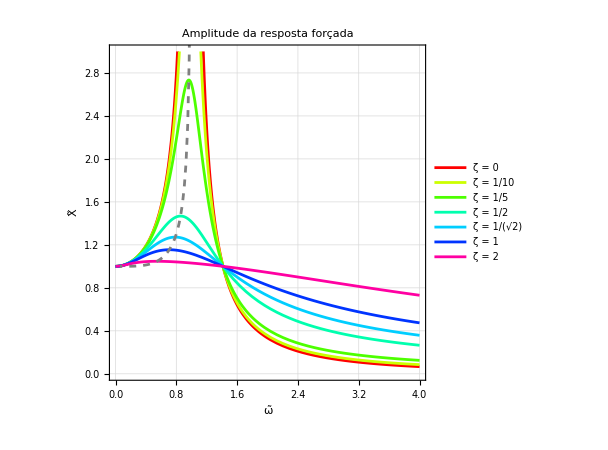
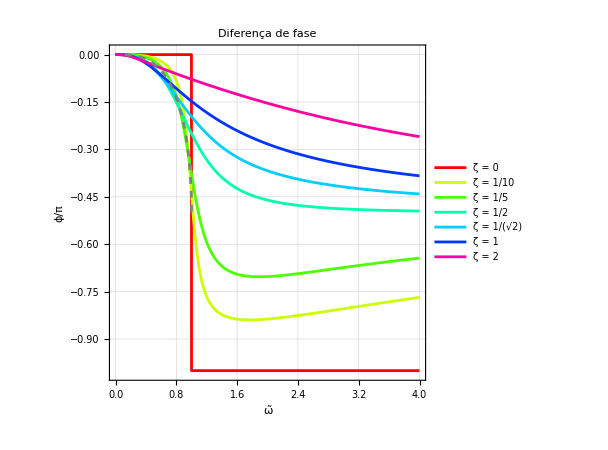

```mathematica
FRO21[foo_,range_,label_,ylabel_,legends_:False]:=Show @@( Flatten @ {
Plot[
(*Abs*)foo[(1+2 ζ s)/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]/.ζ->(#+10^-12),
{ω,0,4},
PlotRange->range(*{0,+3}*),

PlotStyle->{Hue@(√(#/2.5)),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃",ylabel},
PlotLabel->label,
PlotLegends->If[legends,
Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
{}
],

ImageSize->{450,450},
AspectRatio->1
]&/@{0,1/10,1/5,1/2,√2/2,1,2},
{ParametricPlot[
{ω,(*Abs*)foo[(1+2 ζ s)/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]}/.ω->1/2 √((-1+√(1+8 ζ^2))/ζ^2),
{ζ,0,200},
PlotStyle->{Gray,Dashed}
]}
}
)
{{FRO21[Abs,{0,+3},"Amplitude da resposta forçada","X̃",True],
FRO21[Arg[#]/π&,{-1.01,+0.01},"Diferença de fase","ϕ/π",True]}}//Transpose//TableForm
```

```mathematica
Solve[D[(√(1+4 ζ^2 ω^2))/(√(1-2 ω^2+4 ζ^2 ω^2+ω^4)),ω]==0,{ω}]//Simplify
```

{{ω→0},{ω→-1/2 √(-(1+√(1+8 ζ^2))/ζ^2)},{ω→1/2 √(-(1+√(1+8 ζ^2))/ζ^2)},{ω→-1/2 √((-1+√(1+8 ζ^2))/ζ^2)},{ω→1/2 √((-1+√(1+8 ζ^2))/ζ^2)}}

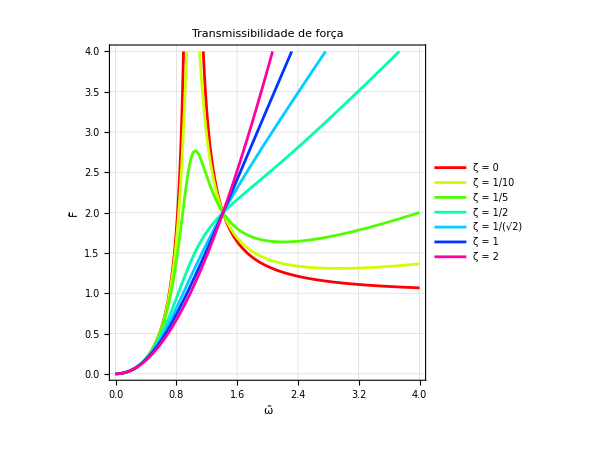
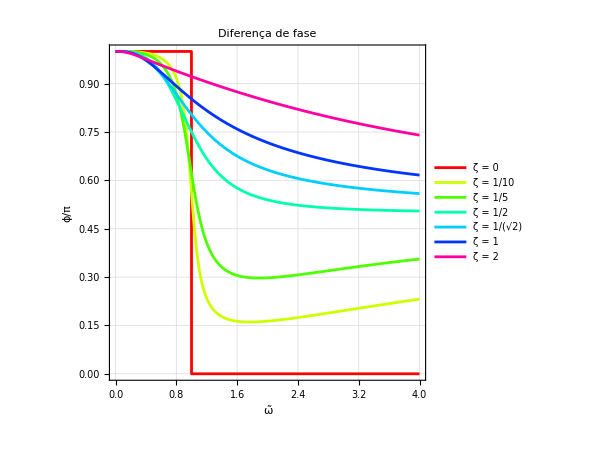

```mathematica
FRO212[foo_,range_,label_,ylabel_,legends_:False]:=Show @@( Flatten @ {
Plot[
(*Abs*)foo[(s^2(1+2 ζ s))/(s^2+2 ζ s+1)/.{s-> ⅈ ω}]/.ζ->(#+10^-12),
{ω,0,4},
PlotRange->range(*{0,+3}*),

PlotStyle->{Hue@(√(#/2.5)),Thick},

GridLines->Automatic,

Frame->True,
FrameLabel->{"ω̃",ylabel},
PlotLabel->label,
PlotLegends->If[legends,
Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
{}
],

ImageSize->{450,450},
AspectRatio->1
]&/@{0,1/10,1/5,1/2,√2/2,1,2}
}
)
{{FRO212[Abs,{0,+4},"Transmissibilidade de força","F̃",True],
FRO212[Arg[#]/π&,{1.01,-0.01},"Diferença de fase","ϕ/π",True]}}//Transpose//TableForm
```

### RESPOSTA NO DOMÍNIO DO TEMPO - EXCITAÇÃO SENOIDAL

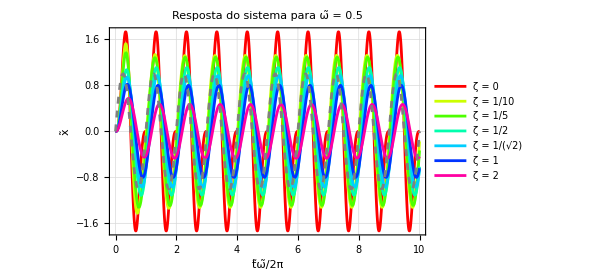

```mathematica
ORO2[ω_]:=Block[{response,plot},
plot=(response=OutputResponse[O2/.{ζ-> #}, Sin[ω t], {t,0,10 2π/ω}];
Plot[
response/.{t->2π τ/ω },
{τ,0,10},
PlotStyle->{Hue@(√(#/2.5)),Thick},
GridLines->Automatic,
Frame->True,
FrameLabel->{"t̃ω̃/2π","x̃"},
PlotLabel->StringForm["Resposta do sistema para ω̃ = ``",ω],
PlotLegends->Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
ImageSize->{450,450}
]
)&/@{0,1/10,1/5,1/2,√2/2,1,2};
Show @@( Flatten @ {
plot,
{Plot[
Sin[2π τ],
{τ,0,10},
PlotStyle->{Gray,Dashed,Thick}]}
})
]
ORO2[0.5]
```

### RESPOSTA NO DOMÍNIO DO TEMPO - DEGRAU UNITÁRIO

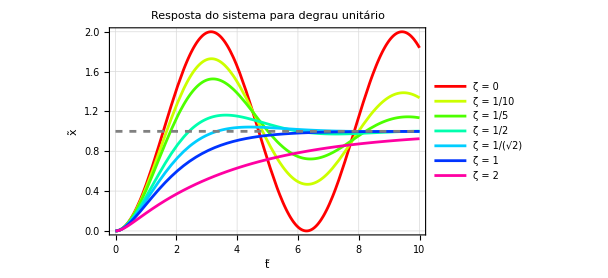

```mathematica
Block[{response,plot},
plot=(response=OutputResponse[O2/.{ζ-> #},UnitStep[t], {t,0,20}];
Plot[
response,
{t,0,10},
PlotStyle->{Hue@(√(#/2.5)),Thick},
GridLines->Automatic,
Frame->True,
FrameLabel->{"t̃","x̃"},
PlotLabel->StringForm["Resposta do sistema para degrau unitário",ω],
PlotLegends->Placed[
 LineLegend[{StringForm["ζ = ``",#]},LegendMarkerSize->30,LabelStyle->{GrayLevel[.4],FontFamily->"Arial",FontSize->16}],
Before
],
ImageSize->{450,450}
]
)&/@{0,1/10,1/5,1/2,√2/2,1,2};
Show @@( Flatten @ {
plot,
{Plot[
UnitStep[t],
{t,0,10},
PlotStyle->{Gray,Dashed,Thick}]}
})
]
```

-Graphics-(Trumper, 2003)